# Calculation of eikonal corrections at KE = 225 MeV for He-4

9/24/13

## Define Constants

```mathematica
mp=0.938272046;(*GeV/c^2*)
mn=1.00137842*mp(*GeV/c^2*);
M=8*mp+8*mn;
m=M/16;
ℏc=0.19732697178(*Giga ElectronVolt*Femto Meter*);
r=.233^(-1/2)(*Femto Meter*);
B=1/4*r^2/ℏc^2(*(c/GeV)^2*);
p=8;
n=8;
A=p+n;
```

```mathematica
En=.225(*GeV*);
EnL=En+mp;
s=mp^2+M^2+2*M*EnL;
ϵ=EnL/(M/Sqrt[s]);
P=Sqrt[EnL^2-mp^2];
k=P*(M/Sqrt[s]);
s2=mp^2+m^2+2*m*EnL;
ϵ2=EnL*(m/Sqrt[s2]);
κ=P*(m/Sqrt[s2]);
ηO=(1-ϵ/M)*(mp+M)/Sqrt[s];
ηD=(1-ϵ/ϵ2+(A-1)*ϵ/M)*(mp+M)/Sqrt[s];
```

## Import data and convert it from degrees and mbarn^1/2 to momentum transfer and fm

```mathematica
pp225a=Import["/Users/Micah/Documents/JerryDuty/eikexp/pp225a.csv"];
pp225b=Import["/Users/Micah/Documents/JerryDuty/eikexp/pp225b.csv"];
```

```mathematica
(*pp225a=Import["/phys/users/mbuuck/JerryDuty/eikexp/pp225a.csv"];
pp225b=Import["/phys/users/mbuuck/JerryDuty/eikexp/pp225b.csv"];*)
```

```mathematica
pp225a=Transpose[{pp225a[[All,1]],pp225a[[All,2]]+I*pp225a[[All,3]]}];
pp225b=Transpose[{pp225b[[All,1]],pp225b[[All,2]]+I*pp225b[[All,3]]}];
```

```mathematica
θpp225=Transpose[{pp225a[[All,1]],(pp225a[[All,2]]+pp225b[[All,2]])/2}];
```

```mathematica
θtoq[x_]:={2 κ Sin[x[[1]] Pi/360],x[[2]]/Sqrt[10]}
```

```mathematica
pp225=θtoq/@θpp225;
```

```mathematica
pn225a=Import["/Users/Micah/Documents/JerryDuty/eikexp/pn225a.csv"];
pn225b=Import["/Users/Micah/Documents/JerryDuty/eikexp/pn225b.csv"];
```

```mathematica
(*pn225a=Import["/phys/users/mbuuck/JerryDuty/eikexp/pn225a.csv"];
pn225b=Import["/phys/users/mbuuck/JerryDuty/eikexp/pn225b.csv"];*)
```

```mathematica
pn225a=Transpose[{pn225a[[All,1]],pn225a[[All,2]]+I*pn225a[[All,3]]}];
pn225b=Transpose[{pn225b[[All,1]],pn225b[[All,2]]+I*pn225b[[All,3]]}];
```

```mathematica
θpn225=Transpose[{pn225a[[All,1]],(pn225a[[All,2]]+pn225b[[All,2]])/2}];
```

```mathematica
pn225=θtoq/@θpn225;
```

```mathematica
NN225=(pp225+pn225)/2;
f=Interpolation[NN225];
fp=Interpolation[pp225];
fn=Interpolation[pn225];
```

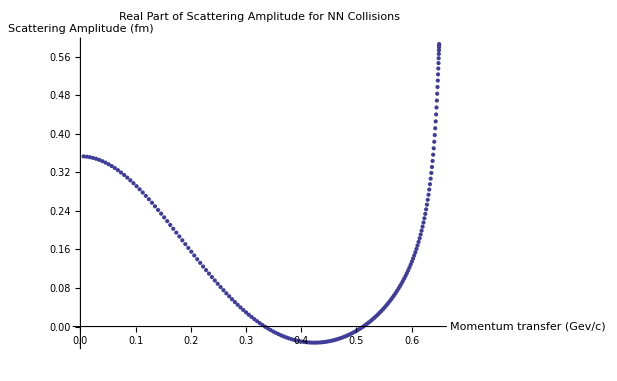

```mathematica
ListPlot[Transpose[{NN225[[All,1]],Re[NN225[[All,2]]]}],PlotLabel->"Real Part of Scattering Amplitude for NN Collisions",AxesLabel->{"Momentum transfer (Gev/c)","Scattering Amplitude (fm)"}]
```

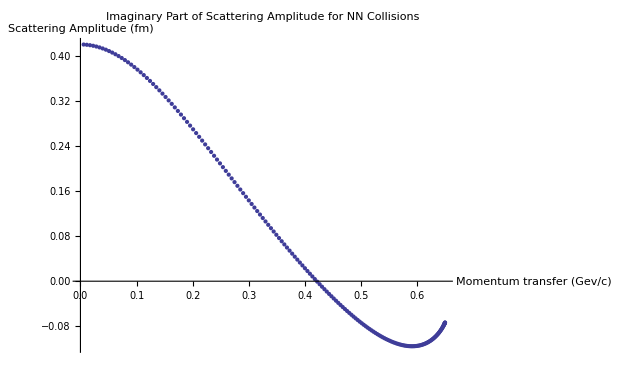

```mathematica
ListPlot[Transpose[{NN225[[All,1]],Im[NN225[[All,2]]]}],PlotLabel->"Imaginary Part of Scattering Amplitude for NN Collisions",AxesLabel->{"Momentum transfer (Gev/c)","Scattering Amplitude (fm)"}]
```

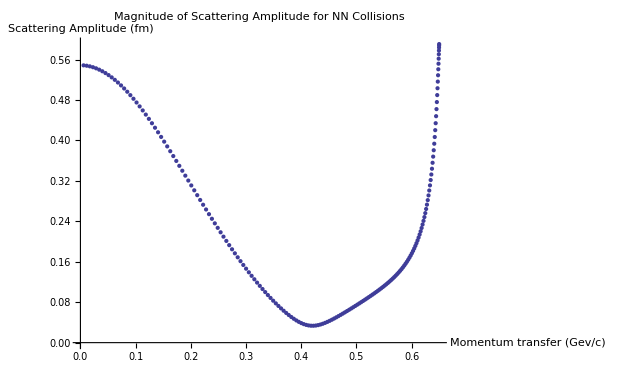

```mathematica
ListPlot[Transpose[{NN225[[All,1]],Abs[NN225[[All,2]]]}],PlotLabel->"Magnitude of Scattering Amplitude for NN Collisions",AxesLabel->{"Momentum transfer (Gev/c)","Scattering Amplitude (fm)"}]
```

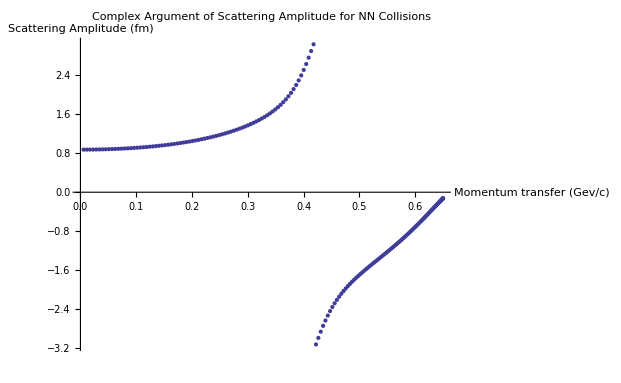

```mathematica
ListPlot[Transpose[{NN225[[All,1]],Arg[NN225[[All,2]]]}],PlotLabel->"Complex Argument of Scattering Amplitude for NN Collisions",AxesLabel->{"Momentum transfer (Gev/c)","Scattering Amplitude (fm)"}]
```

## Fit data to complex gaussian (see model on next line)

```mathematica
Clear[β,ρ,σ]
model=κ σ (I+ρ)/(4 Pi) Exp[-β q^2];
```

The fit is only performed over the first 50 degrees.

{a→0.549776,βre→14.2078}

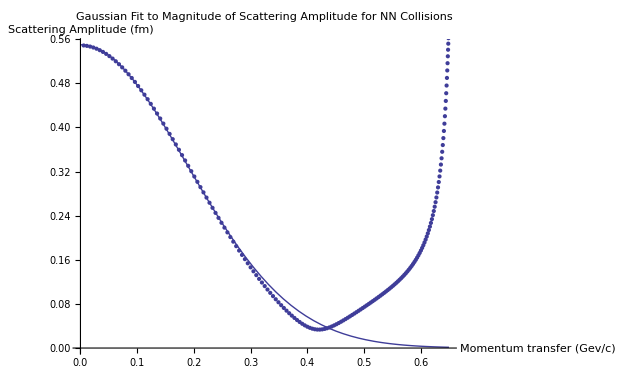

```mathematica
Npts=50;
FindFit[Transpose[{NN225[[1;;Npts,1]],Abs[NN225[[1;;Npts,2]]]}],a Exp[-βre q^2],{a,βre},q]
Show[Plot[a Exp[-βre q^2]/.%,{q,0,2 κ}],ListPlot[Transpose[{NN225[[All,1]],Abs[NN225[[All,2]]]}]],PlotLabel->"Gaussian Fit to Magnitude of Scattering Amplitude for NN Collisions",AxesLabel->{"Momentum transfer (Gev/c)","Scattering Amplitude (fm)"}]
```

{ρ→0.859308,βim→-4.9207}

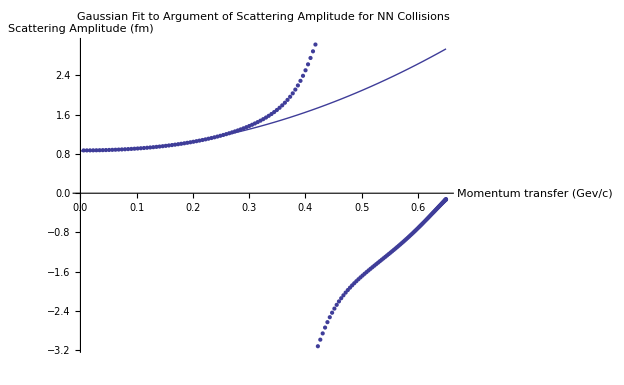

```mathematica
FindFit[Transpose[{NN225[[1;;Npts,1]],Arg[NN225[[1;;Npts,2]]]}],ArcTan[ρ,1]-βim q^2,{ρ,βim},q]
Show[ListPlot[Transpose[{NN225[[All,1]],Arg[NN225[[All,2]]]}]],Plot[ArcTan[ρ,1]-βim q^2/.%,{q,0,2 κ}],PlotLabel->"Gaussian Fit to Argument of Scattering Amplitude for NN Collisions",AxesLabel->{"Momentum transfer (Gev/c)","Scattering Amplitude (fm)"}]
```

```mathematica
NSolve[κ/ℏc σ Sqrt[1+ρ^2]/(4 Pi)==0.5497756862779463&&ρ==0.859307976650379,{σ,ρ}]
```

{{σ→3.18138,ρ→0.859308}}

Fitted parameters:

```mathematica
σ=3.181379501307418;
ρ=0.859307976650379;
β=14.207765926135037-4.920698581212597 I;
```

## Glauber

```mathematica
σ1=-σ/ℏc^2 (1-I ρ)/(8 Pi β)
Fcm[q_]:=Exp[B*q^2/A]
```

-0.265108+0.104802 ⅈ

```mathematica
F0225[q_]:=-2*I*k*Fcm[q]*(B+β)*Sum[Binomial[A,j]/j*(-σ (1-I ρ)/ℏc^2/(8 Pi (B+β)))^j*Exp[-(B+β)*q^2/j],{j,1,A}]*ℏc
```

Glauber approximation  for p-α scattering is below:

```mathematica
40*Pi/(k/ℏc) Im[F0225[0]]
```

427.682

```mathematica
ρ0[q_]:=Exp[-B q^2]
```

InterpolatingFunction::dmval: Input value {0.00293792} lies outside the range of data in the interpolating function. Extrapolation will be used.

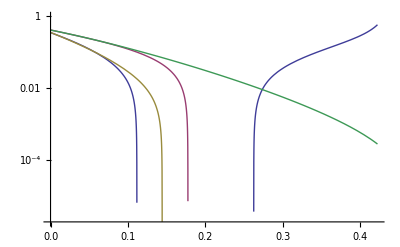

```mathematica
LogPlot[{Re[f[Sqrt[q]]],Im[f[Sqrt[q]]],Re[κ/ℏc σ (I+ρ)/(4 Pi) Exp[-β Sqrt[q]^2]],Im[κ/ℏc σ (I+ρ)/(4 Pi) Exp[-β Sqrt[q]^2]]},{q,0,(2 κ)^2}]
```

InterpolatingFunction::dmval: Input value {0.00293792} lies outside the range of data in the interpolating function. Extrapolation will be used.

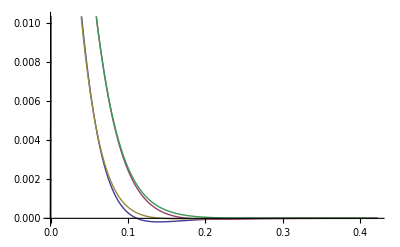

```mathematica
Plot[{Re[Sqrt[q]f[Sqrt[q]] ρ0[Sqrt[q]]],Im[Sqrt[q] f[Sqrt[q]] ρ0[Sqrt[q]]],Re[Sqrt[q] κ/ℏc σ (I+ρ)/(4 Pi) Exp[-β Sqrt[q]^2] ρ0[Sqrt[q]]],Im[Sqrt[q] κ/ℏc σ (I+ρ)/(4 Pi) Exp[-β Sqrt[q]^2] ρ0[Sqrt[q]]]},{q,0,(2 κ)^2}]
```

```mathematica
Γp225=Interpolation[Table[{b,1/(I κ) NIntegrate[ρ0[q] BesselJ[0,b q] fp[q]/ℏc q,{q,0,2 κ}]},{b,0,50}]];
Γn225=Interpolation[Table[{b,1/(I κ) NIntegrate[ρ0[q] BesselJ[0,b q] fn[q]/ℏc q,{q,0,2 κ}]},{b,0,50}]];
```

```mathematica
Γ225[b_]=(Γp225[b]+Γn225[b])/2;
```

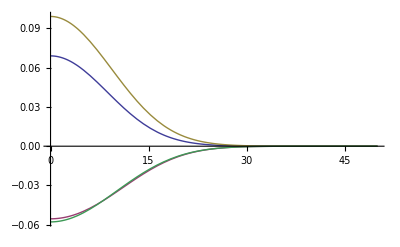

```mathematica
Plot[{Re[Γp225[b]],Im[Γp225[b]],Re[Γn225[b]],Im[Γn225[b]]},{b,0,50},PlotRange->All]
```

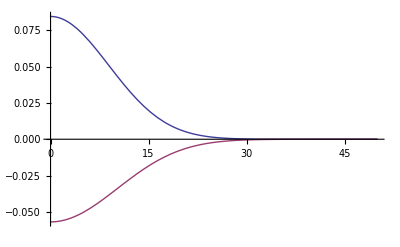

```mathematica
Plot[{Re[σ/ℏc^2 (1-I ρ)/(4B) Exp[-b^2/(4B)/(1+β/B)]/(2 Pi (1+β/B))],Im[σ /ℏc^2(1-I ρ)/(4B) Exp[-b^2/(4B)/(1+β/B)]/(2 Pi (1+β/B))]},{b,0,50},PlotRange->All]
```

```mathematica
Γ[0]
```

-0.265108+0.104802 ⅈ

```mathematica
Clear[U225]
```

```mathematica
U225temp[q_]:=2*Pi*I*NIntegrate[b*BesselJ[0,b*q]*Log[1-σ1 Exp[-b^2/(4 β)]],{b,0,Infinity}]
```

```mathematica
U225=Quiet[Interpolation[Table[{q,U225temp[q]},{q,0,2 κ,.01}]]];
```

```mathematica
γ=100*Quiet[(Log[U225[0]]-Log[U225[0.1]])]
```

14.6008-5.24662 ⅈ

```mathematica
Z=U225[0]/(-I*4*Pi*σ1*β)(*Unitless*)
```

0.939721+0.0211142 ⅈ

```mathematica
γ1:=γ*β/(γ+β)(*(c/GeV)^2*)
αnL[n_,L_]:=If[n==1,(2*(γ+B)^-1+L*(β+B)^-1)^-1,If[n==2,((γ+B)^-1+(γ1+B)^-1+L*(β+B)^-1)^-1,If[n==3,(2*(γ1+B)^-1+L*(β+B)^-1)^-1]]]
an[n_]:=If[n==1,(γ+B)^-2,If[n==2,-2*σ1*(γ1/γ)*(γ+B)^-1*(γ1+B)^-1,If[n==3,σ1^2*(γ1/γ)^2*(γ1+B)^-2]]]
bn[n_]:=If[n==1,(γ+B)^-3,If[n==2,-σ1*(γ1/γ)*(γ1+B)^-1*(γ+B)^-1*((1-B*γ1/(β*(B+γ1)))/(γ+B)+(1-γ1/β)/(γ1+B)),If[n==3,σ1^2*(γ1/γ)^2*(γ1+B)^-3*(1-B*γ1/(β*(B+γ1)))*(1-γ1/β)]]]
γ2:=γ*β/(β+γ/2)(*(c/GeV)^2*)
βnL[n_,L_]:=If[n==1,((γ/2+B)^-1+L*(β+B)^-1)^-1,If[n==2,((γ2/2+B)^-1+L*(β+B)^-1)^-1]]
cn[n_]:=If[n==1,(γ-2*B)*(γ+2*B)^-2,If[n==2,-σ1(γ2/γ)*(γ2+2*B)^-1*(1-2*γ2/γ+2*(γ2)^2/(γ*(γ2+2*B)))]]
dn[n_]:=If[n==1,γ*(γ+2*B)^-3,If[n==2,
-σ1*(γ)^-2*(γ2/(γ2+2*B))^3]]
```

```mathematica
FO1225[q_(*c/GeV*)]:=A*(A-1)*Fcm[q]*ηO*(β*σ1*Z)^2/(2*(2*Pi*(B+γ))^(1/2))*Sum[Binomial[A-2,L]*(-σ1*β/(B+β))^L*Sum[αnL[n,L]*(an[n]-4*αnL[n,L]*bn[n]*(1-αnL[n,L]q^2))*Exp[-αnL[n,L]*q^2],{n,1,3}],{L,0,A-2}]*ℏc
```

```mathematica
FD1225[q_(*c/GeV*)]:=A*Fcm[q]*ηD*(β*σ1*Z)^2/(2*γ*Sqrt[2*Pi*γ])*Sum[Binomial[A-1,L]*(-σ1*β/(B+β))^L*Sum[βnL[n,L]*(cn[n]-4*βnL[n,L]*dn[n]*(1-βnL[n,L]*q^2))*Exp[-βnL[n,L]*q^2],{n,1,2}],{L,0,A-1}]*ℏc
```

Using parameterized NN scattering amplitude:

```mathematica
40*Pi/(k/ℏc) Im[F0225[0]]
```

427.682

```mathematica
40*Pi/(k/ℏc) Im[F0225[0]+FO1225[0]+FD1225[0]]
```

438.862

Using exact NN scattering amplitude (average of pp and pn):

```mathematica
40 Pi/(k/ℏc) Im[I k ℏc NIntegrate[b BesselJ[0,0](1-(1-Γ225[b])^A),{b,0,50}]]
```

430.806

Using exact scattering amplitude for pp and pn:

```mathematica
40 Pi/(k/ℏc) Im[I k ℏc NIntegrate[b BesselJ[0,0](1-(1-Γp225[b])^p(1-Γn225[b])^n),{b,0,50}]]
```

431.023

Fractional correction from using exact scattering amplitude:

```mathematica
Im[F0225[0]-I k ℏc NIntegrate[b BesselJ[0,0](1-(1-Γp225[b])^p(1-Γn225[b])^n),{b,0,50}]]/Im[F0225[0]]
```

-0.00781139

```mathematica
dσdΩ[q_]:=Abs[I k ℏc NIntegrate[b BesselJ[0,b q](1-(1-Γp225[b])^p(1-Γn225[b])^n),{b,0,50}]]^2
```

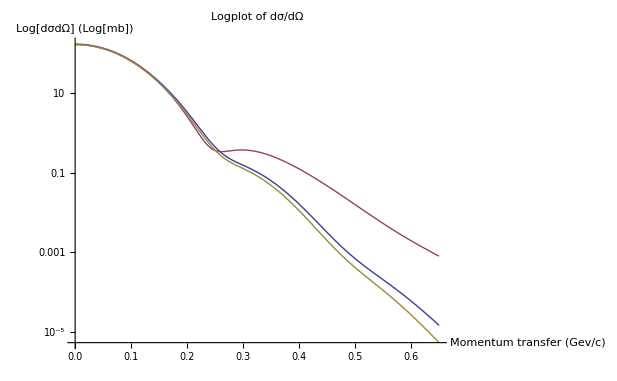

```mathematica
LogPlot[{Abs[F0225[q]]^2,Abs[F0225[q]+FO1225[q]+FD1225[q]]^2,dσdΩ[q]},{q,0,2κ},PlotLabel->"Logplot of dσ/dΩ",AxesLabel->{"Momentum transfer (Gev/c)","Log[dσdΩ] (Log[mb])"}]
```